# 38b: PreconditionedConjugate Gradients

## A.x=b via Conjugate Gradients

For A ϵ ℝ^(m×m) is Symmetric and Positive Definite (SPD) ||x(||)_(CG(A)):=√(x.A.x) is a norm!   Conjugate Gradients iteratively minimizes the residual in this tailored norm.

### Algorithm 38.1

Conjugate gradients (Algorithm 38.1) is simply this exact line search minimization starting from the predetermined  initial guess x_0=OverVector[0].  Here is the pseudo code from the text

Conjugate Gradients
x_0=0, r_0=b, p_0=r_0
for n in 1, 2, 3, ...
	α_n=(r_(n-1).r_(n-1))/(p_(n-1).A.p_(n-1))
	x_n=x_(n-1)+α_n p_(n-1)
	r_n=r_(n-1)-α_n A.p_(n-1)
	β_n=(r_n.r_n)/(r_(n-1).r_(n-1))
	p_n=r_n+β_n p_(n-1)

Here is an implementation of a single step

```mathematica
CGStep[A_][{xIn_,rIn_,pIn_}]:=Module[{ApIn=A.pIn,α,β,xOut,rOut,pOut},
α=(rIn.rIn)/(pIn.ApIn);
xOut=xIn+α pIn;
rOut=rIn - α ApIn;
β = (rOut.rOut)/(rIn.rIn); 
pOut=rOut+β pIn;
{xOut,rOut,pOut}]

CGNorm[A_][x_]:= √(x.A.x)
```

Import an SPD matrix A from Matrix market, define a synthetic solution x_∞, and compute the matching RHS.

```mathematica
A=Import[
"https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc1/bcsstk05.mtx.gz"];
m=Length[A];
(* Create an identifiable synthetic solution and matching RHS *)
xInf=Table[Cos[0.1 i],{i,m}];b=A.xInf;
(* Initialize and run CG loop *)
MaxIter=50;
{x0,r0,p0}={0*b, b,b};
xrpData=NestList[CGStep[A],{x0,r0,p0},MaxIter];
(* Visualize the Convergence *)
TabView[{
"x_MaxIter"->ListPlot[{xrpData⟦-1,1⟧,xInf}],
"||x-x_∞(||)_(CG (A))"->ListLogPlot[Map[CGNorm[A][#-xInf]&,xrpData⟦All,1⟧]],
"||x-x_∞(||)_2"->ListLogPlot[Map[Norm[#-xInf]&,xrpData⟦All,1⟧]],
"||r||"->ListLogPlot[Map[Norm,xrpData⟦All,2⟧]]
}]
```

1234

Slow but very steady is what I would say here. Remember, preconditioners are essential!

```mathematica
TabView[{
"Diagonal A"->ListLogPlot[Diagonal[A],PlotRange->All],
"A"->MatrixPlot[A,PlotLegends->Automatic]}]
```

12

## Preconditioners

For CG to make sense we need the iteration matrix to be SPD.  We know exactly two preconditioners: Jacobi and ILU.  We are going to write code for another Incomplete Cholesky appropriate for SPD problems. As a reminder, the diagonal entries of an SPD matrix must be positive!  Here is a small SPD matrix from Matrix Market which has mostly pretty large diagonal entries!

Import an SPD matrix A from Matrix market, define a synthetic solution x_∞, and compute the matching RHS.

```mathematica
A=Import[
"https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc1/bcsstk05.mtx.gz"];
m=Length[A];
(* Create an identifiable synthetic solution and matching RHS *)
xInf=Table[Cos[0.1 i],{i,m}];b=A.xInf;
(* Initialize and run CG loop *)
MaxIter=12;
{x0,r0,p0}={0*b, b,b};
xrpData=NestList[CGStep[A],{x0,r0,p0},MaxIter];
(* Visualize the Convergence *)
TabView[{
"x_MaxIter"->ListPlot[{xrpData⟦-1,1⟧,xInf}],
"||x-x_∞(||)_(CG (A))"->ListLogPlot[Map[CGNorm[A][#-xInf]&,xrpData⟦All,1⟧]],
"||x-x_∞(||)_2"->ListLogPlot[Map[Norm[#-xInf]&,xrpData⟦All,1⟧]],
"||r||"->ListLogPlot[Map[Norm,xrpData⟦All,2⟧]]
}]
```

1234

It is converging but we should see if we can make it faster!

One way to make the modified iteration matrix for CG Symmetric is to multiply on both sides. If we define 
	S = SparseArray[Diagonal[A]^(-1/2), {m, m}]
so that S^2 is the original Jacobi preconditioner we used for an ILU then solving 
	A.x=b ⟺S.A.x=S.b ⟺S.A.S.y=S.b where S.y=x.
Since S is diagonal the matrix S.A.S=S.A.Sᵀ is symmetric and the final step x=S.y to find x is very inexpensive.  Lets compare the eigenvalues of (all real and positive) the original and transformed matrices

```mathematica
A=Import[
"https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc1/bcsstk05.mtx.gz"];
m=Length[A];
S=SparseArray[Band[{1,1}]->1/√Normal[Diagonal[A]],{m,m}];SAS=S.A.S; InvS=Inverse[S];
{λA,λSAS}= Map[Eigenvalues,Normal[{A,SAS}]];
{κA,κSAS}=Map[Max[#]/Min[#]&,{λA,λSAS}];
ListLogPlot[{λA,λSAS},
PlotLegends->{"A","SAS"},
PlotLabel->StringForm["Condition Numbers = ``",{κA,κSAS}]
];
MaxIter=12;
(* Create an identifiable Answer and the matching RHS *)
xInf=Table[Cos[0.1 i],{i,m}];
b=A.xInf;
Sb=S.b;
yInf=Inverse[S].xInf;
(* Compute CG data for SAS *)
Clear[yrpData]
{y0,r0,p0}={0*Sb, Sb,Sb};
yrpData=NestList[CGStep[SAS],{y0,r0,p0},MaxIter];
xData=Table[y=yrpData⟦i,1⟧;S.y,{i,Length[yrpData]}];
TabView[{
"x_MaxIter"->ListPlot[{xData⟦-1⟧,xInf}],
"||y-y_∞(||)_CG"->ListLogPlot[Map[CGNorm[SAS][#-yInf]&,yrpData⟦All,1⟧],AxesLabel->{"n","||y-y_∞(||)_CG"}],
"||y-y_∞(||)_2"->ListLogPlot[Map[Norm[#-yInf]&,yrpData⟦All,1⟧],AxesLabel->{"n","||y-y_∞(||)_2"}],
"||r||"->ListLogPlot[Map[Norm,yrpData⟦All,2⟧],AxesLabel->{"n","||r||"}]
}]
```

1234

Better but not good.  An Incomplete Cholesky (IC)  decomposition A≈Uᵀ.U for SPD matrices analogous to the Incomplete LU (ILU)  decomposition A≈L.U would be useful because we could iterate with 		
	(U^-1)ᵀ.A.(U^-1)≈(U^-1)ᵀ.Uᵀ.U.(U^-1)≈I.  
The no-fill Incomplete Cholesky decomposition produces a upper triangular matrix U with the same sparsity pattern as the input.  We are going to modify our first (row oriented) Cholesky decomposition below to only update the originally non-zero entries.  Here is our old row oriented standard Cholesky.

Book Cholesky (from before)

R=A
for k in 1:m
	for j in k+1:m
		R[j,j:m]=R[j,j:m]-R[k,j:m]*R[k,j]/R[k,k]
	end
	R[k,k:m]=R[k,k:m]/sqrt(R[k,k])
end
triu!(R)

All I really need to do to make it an incomplete Cholesky is modify the inner loop to only update the non-default entries of an existing sparse vector. Since Mathematica stores sparse arrays as a list of  sparse rows this is the natural way to do it.

We need to replace the inner loop action
	R[j,j:m]=R[j,j:m]-R[k,j:m]*R[k,j]/R[k,k]
with a specialized sparse vector variant. Basic linear algebra operations like above are coded up as extremely efficient BLAS. Here is a link to the wiki page discussing BLAS 
	https://en.wikipedia.org/wiki/Basic_Linear_Algebra_Subprograms
which stands for Basic Linear Algebra Subroutines.  The most common CPU BLAS distributions are the Intel MKL library. Here is the the reference page for the ?axpy routines in the MKL library
	www.intel.com/content/www/us/en/develop/documentation/onemkl-developer-reference-fortran/top/blas-and-sparse-blas-routines/blas-routines/blas-level-1-routines-and-functions/axpy.html

So axpy(x,y,α) performs an efficient in-place y←y+α x

In case anyone cares axpy is a mnemonic for “a x plus y”

Our inner update looks like axpy(R[k,j:m],R[j,j:m],-R[k,j]/R[k,k])

We are going to define a sparse version that only updates the non-zero entries in “y”.

First I am going to check that I can make my own  axpy and use it in a Cholesky decomposition

```mathematica
SetAttributes[axpy, HoldAll]
axpy[x_,y_,a_]:= Module[{},y=y+a*x]
DenseChol[A_]:= Module[{R=A,m=Length[A]},
Do[
Do[ 
axpy[R⟦k,j;;m⟧,R⟦j,j;;m⟧,-R⟦k,j⟧/R⟦k,k⟧],
{j,k+1,m}];
R⟦k,k;;m⟧=R⟦k,k;;m⟧/Sqrt[R⟦k,k⟧],
{k,1,m}];
UpperTriangularize[R]
]
```

Testing

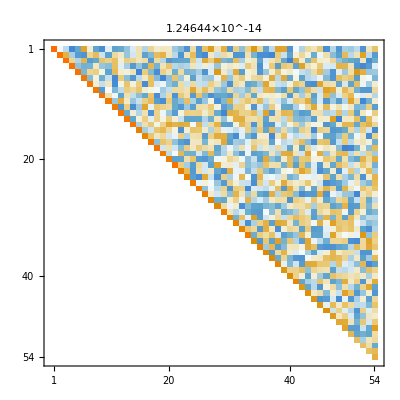

```mathematica
m=54;
A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ;
U=DenseChol[A];
MatrixPlot[U,PlotLabel->Norm[A-Uᵀ.U]]
```

### Sparse Vector Updates

To make the sparse axpy we need to work out how to look inside a sparse vector efficiently. Fortunately, everything you could possibly want to know about sparse vectors/matrices can be efficiently extracted using various “Methods”. Most are fairly self-explanatory. We only care about where and what the non-zero values are!

```mathematica
y=SparseArray[{2->2.3,5->3.4,12->24},24]
y["Methods"]
```

SparseArray[…]

{AdjacencyLists,Background,BandWidth,ColumnIndices,Density,MatrixColumns,MethodInformation,Methods,NonzeroPositions,NonzeroValues,PatternArray,PatternValues,Properties,RowPointers}

A sparse “axpy” that updates the specified entries in a sparse vector v and leaves the zeros alone needs to:

Identify the non zero positions of y.

Extract the x entries in those positions.

Multiply the x entries by a and add them to the appropriate locations of y.

The following code does this and can be switched in for the axpy code above to make an incomplete Cholesky.

```mathematica
SetAttributes[ZeroPreservingSparseAXPY,HoldAll]
ZeroPreservingSparseAXPY[x_,y_,a_]:= Module[{nzp},
nzp=Flatten[y["NonzeroPositions"]];
y⟦nzp⟧=y⟦nzp⟧+a*x⟦nzp⟧;
]
```

Test with dense x.

```mathematica
m=24;
y=SparseArray[{2->2.3,5->3.4,12->24},m];
x=RandomReal[{-1,1},m];
a=1.2;
ZeroPreservingSparseAXPY[x,y,a]
Normal[y]
```

{0,2.93789,0,0,4.12691,0,0,0,0,0,0,24.8526,0,0,0,0,0,0,0,0,0,0,0,0}

Test with Sparse x

```mathematica
m=24;
y=SparseArray[{2->2.3,5->3.4,12->24},m];
x=SparseArray[{2->3.3,4->12.2},m];
a=1.2;
ZeroPreservingSparseAXPY[x,y,a]
Normal[y]
```

{0,6.26,0,0,3.4,0,0,0,0,0,0,24.,0,0,0,0,0,0,0,0,0,0,0,0}

Build out an Incomplete Cholesky R[j,j:m]=R[j,j:m]-R[k,j:m]*R[k,j]/R[k,k]

```mathematica
IncompleteChol[A_]:= Module[{R=A,m=Length[A],nzp},
Do[
Do[ 
nzp=Flatten[R⟦j,j;;m⟧["NonzeroPositions"]];
R⟦j,nzp⟧=R⟦j,nzp⟧-R⟦k,nzp⟧*R⟦k,j⟧/R⟦k,k⟧ ,
{j,k+1,m}];
R⟦k,k;;m⟧=R⟦k,k;;m⟧/Sqrt[R⟦k,k⟧],
{k,1,m}];
UpperTriangularize[R]
]
```

Testing

```mathematica
A=Import[
"https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc1/bcsstk05.mtx.gz"];
IR=IncompleteChol[A]
R=CholeskyDecomposition[A];
```

SparseArray[…]

SparseArray[…]

```mathematica
TabView[{
"R"->MatrixPlot[R,PlotLegends->Automatic],
"IR"->MatrixPlot[IR,PlotLegends->Automatic],
"A-Rᵀ.R"->MatrixPlot[A-Rᵀ.R,PlotLegends->Automatic],
"A-IRᵀ.IR"->MatrixPlot[A-IRᵀ.IR,PlotLegends->Automatic]
}
]
```

1234

## IChol as a Preconditioner.

We now have two preconditioners!  Here are the spectra.

SparseArray[…]

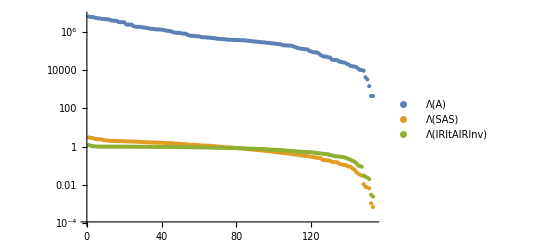

```mathematica
S=SparseArray[Band[{1,1}]->1/√Diagonal[Normal[A]]]
SAS=Normal[S.A.S];
IRInv=Inverse[Normal[IR]];
IRItAIRInv=IRInvᵀ.Normal[A].IRInv;
ListLogPlot[{Eigenvalues[Normal[A]],Eigenvalues[SAS],Eigenvalues[IRItAIRInv]},
PlotLegends->{"Λ(A)","Λ(SAS)","Λ(IRItAIRInv)"},PlotRange->All]
```

It is worth looking at the Cholesky spectrum on its own.

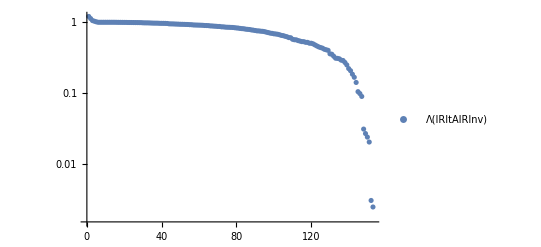

```mathematica
ListLogPlot[Eigenvalues[IRItAIRInv],
PlotLegends->{"Λ(IRItAIRInv)"},PlotRange->All]
```

# Power Series Motivation

A different idea is to see which entries are (or maybe should be big).  Since A is SPD the diagonal entries are positive and can perform a symmetric scaling to make all the diagonal entries 1.  This is just the symmetric variant of the Jacobi preconditioner we looked at before.

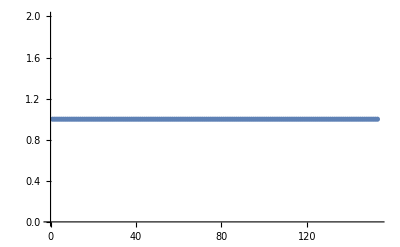

```mathematica
A=Import[
"https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc1/bcsstk05.mtx.gz"];
m=Length[A];
S=SparseArray[Band[{1,1}]->Normal[Diagonal[A]]^(-1/2)];
A0=S.A.S;ListPlot[Diagonal[A0]]
```

So now 
	A_0=Id + A_1
where all diagonal entries of A_1 are zero!  The power series (called a Neumann series in this context) gives
	(A_0)^-1=(Id+A_1)^-1=Id-A_1+A_1.A_1-A_1.A_1.A_1+…  
which converges fast (we do not need to add up many terms) if A_1 is small.  It is not obvious how to make this a symmetric preconditioner suitable for CG. What we want is an approximation R≈(A_0)^(-1/2) so that R.A_0.R≈Id.  The power series
	(A_0)^(-1/2)=(Id+A_1)^(-1/2)=Id-1/2 A_1+3/8 A_1^2-5/16 A_1^3+35/128 A_1^4+…
converges fast provided A_1is small.  Lets see how these would do as preconditioners.

```mathematica
Clear[R]
Id=SparseArray[Band[{1,1}]->1,Dimensions[A0]];
A1=A0-Id;
R1=Id-1/2 A1;
R2 = R1+3/8 A1.A1;
R3=R2-5/16 A1.A1.A1;
R4=R3+35/128 A1.A1.A1.A1;
TabView[{
"A0"->MatrixPlot[A0],
"R1"->MatrixPlot[R1],
"R2"->MatrixPlot[R2],
"R3"->MatrixPlot[R3],
"R4"->MatrixPlot[R4]
}];
λs={
Eigenvalues[R1.A0.R1],
Eigenvalues[R2.A0.R2],
Eigenvalues[R3.A0.R3],
Eigenvalues[R4.A0.R4]
};
TabView[Table[
i->ListPlot[λs⟦i⟧,Joined->True,PlotRange->All],
{i,1,4}]]
```

1234

This thought process suggests that we might be able to use the sparsity patterns of powers of A as templates for approximate inverses.  In almost all circumstances the footprint of powers of A grow rapidly.  ILU(2) uses computes only the footprint of A^2.

```mathematica
TabView[{
"A"->MatrixPlot[A,PlotLegends->Automatic],
"A.A"->MatrixPlot[A.A,PlotLegends->Automatic],
"A.A.A"->MatrixPlot[A.A.A,PlotLegends->Automatic],
"A.A.A.A"->MatrixPlot[A.A.A.A,PlotLegends->Automatic]
}]
```

1234